# Kronecker Graphs

```mathematica
Clear["Global`*"]
n=4;
K1=Table[0,{i,1,n},{j,1,n}];
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
x=RandomVariate[BernoulliDistribution[0.5]];
K1[[i,j]]=x;
K1[[j,i]]=x;
];];
MatrixForm[K1]
```

(0 | 1 | 0 | 0
1 | 0 | 1 | 1
0 | 1 | 0 | 1
0 | 1 | 1 | 0)

```mathematica
K[1]=K1;
K[k_]:=KroneckerProduct[K[k-1],K[1]];
```

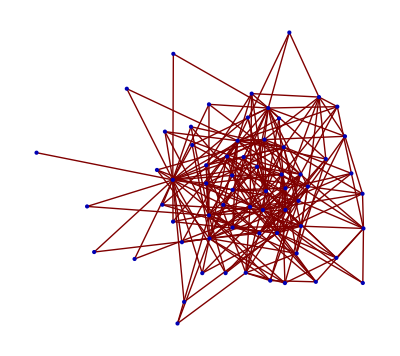

```mathematica
GraphPlot[K[3]]
```

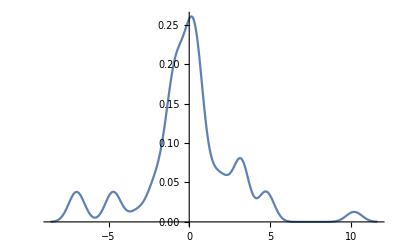

```mathematica
eigs=Eigenvalues[K[3]]//N;
SmoothHistogram[eigs,PlotRange->All]
```

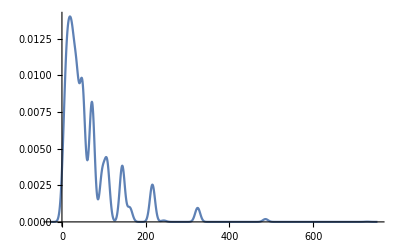

```mathematica
SmoothHistogram[VertexDegree[AdjacencyGraph[K[6]]],PlotRange->All]
```